# Pchem Assignment 5 – 7 November 2016

```mathematica
Directory[]
```

/Users/Research

```mathematica
tdnatall = Transpose[Import[ "/Users/Research/JHU_Class_Material/pchem/assignment_5/TDenat.xlsx","Data"]];
tdnat=Transpose[tdnatall[[2;;]]][[1]]
```

{{20.,384827.},{24.,378109.},{28.,368302.},{32.,351668.},{36.,337514.},{40.,313397.},{44.,268746.},{48.,178369.},{52.,81084.4},{56.,46140.6},{60.,36678.5},{64.,33935.7},{68.,29980.3},{72.,28432.7}}

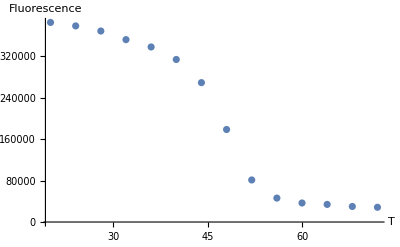

```mathematica
(*Plot the denaturation data*)
tdnatplot=ListPlot[tdnat,PlotRange->All,AxesLabel->{"T","Fluorescence"}]
```

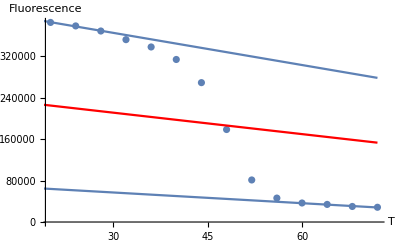

```mathematica
(*Fit the denaturation data to two baselines. So Tm is around 48*)
ln=LinearModelFit[tdnat[[1;;3]],x,x];
lu=LinearModelFit[tdnat[[-3;;]],x,x];
Show[tdnatplot,Plot[ln[x],{x,0,72}],Plot[lu[x],{x,0,72}],Plot[((ln[x]-lu[x])/2)+lu[x],{x,0,72},PlotStyle->Red]]
```

```mathematica
(*Doug's thing*)
(*part b then needs the b/a thing that gets Keq and then you get dG from that*)
chemdenat1 = Transpose[Transpose[Import[ "/Users/Research/JHU_Class_Material/pchem/assignment_5/chemdenatdata1","Data"]][[3;;]]][[1]];
normalizedchemdenat=Table[
```

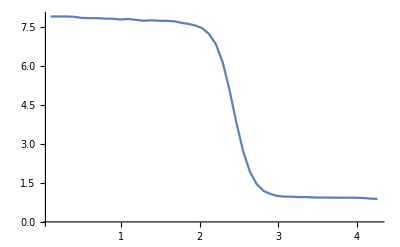

```mathematica
ListLinePlot[chemdenat1,PlotRange->All]
```